Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210421_OR_model_and_other_lines_sliding"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
datafull=Import["../data/csp_manipulated_211512.csv"];
```

Data with Sliding Time Windows

```mathematica
x1=Round@Ceiling[Length@datafull/10,1];
{a,b,c,d,e,f,g,h,i,j}=Join[Range[x1,Length@datafull,x1],{Length@datafull}];
data1=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x1/2,z[[2]]-x1/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i,j},2,1]}],1]];
win1=Length@data1;
```

```mathematica
x2=Round@Ceiling[Length@datafull/20,1];
{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t,u}=Join[Range[x2,Length@datafull,x2],{Length@datafull}];
data2=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x2/2,z[[2]]-x2/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t,u},2,1]}],1]];
win2=Length@data2;
```

Investigation of Constraints Impact in Time Windows

Fixed Step Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep1=snetworkdatabinnedintimewindows[data1,9,11,win1];]
```

{103.894,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep1[[1]][[i]],widthdataintimewindowsFixedstep1[[2]][[i]],2,7,400,Green],{i,Range@win1}];
modularityvalues1=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity1=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{299.254,Null}

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep2=snetworkdatabinnedintimewindows[data2,9,11,win2];]
```

{60.2338,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep2[[1]][[i]],widthdataintimewindowsFixedstep2[[2]][[i]],2,7,400,Green],{i,Range@win2}];
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity2=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{998.196,Null}

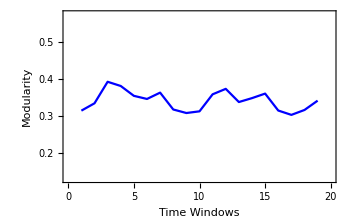
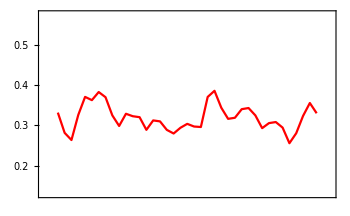
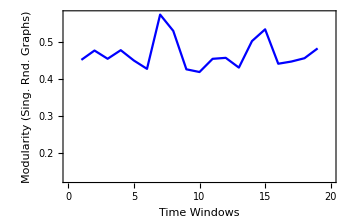
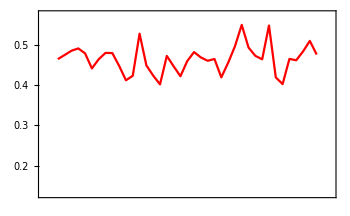
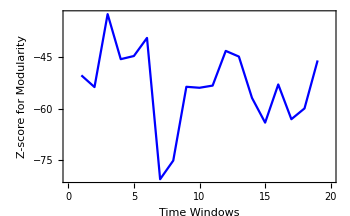
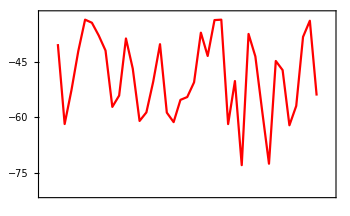

```mathematica
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{0.13,0.575}}],ListLinePlot[Thread[{Range@win2,modularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{0.13,0.575}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,singlerandomcommmodularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{0.13,0.575}}],ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{0.13,0.575}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,Zscoresmodularity1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-score for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},MinMax[{Zscoresmodularity1,Zscoresmodularity2}]}],ListLinePlot[Thread[{Range@win2,Zscoresmodularity2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},MinMax[{Zscoresmodularity1,Zscoresmodularity2}]}]}]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep1=snetworkdatabinnedintimewindows[data1,10,0.05,win1];]
```

{202.782,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedstep1[[1]][[i]],thicknessdataintimewindowsFixedstep1[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win1}];
modularityvalues1=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity1=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{102.559,Null}

```mathematica
N@Mean@graphsandnodenumbers[[All,2]]
```

21.6842

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep2=snetworkdatabinnedintimewindows[data2,10,0.05,win2];]
```

{211.166,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedstep2[[1]][[i]],thicknessdataintimewindowsFixedstep2[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win2}];
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity2=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{334.386,Null}

```mathematica
N@Mean@graphsandnodenumbers[[All,2]]
```

18.2308

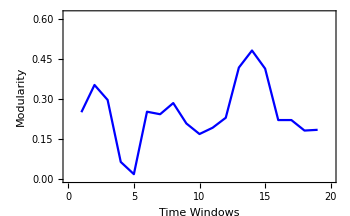
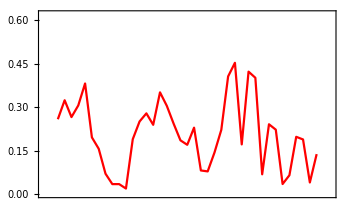
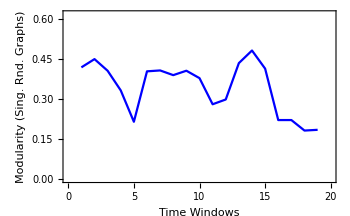
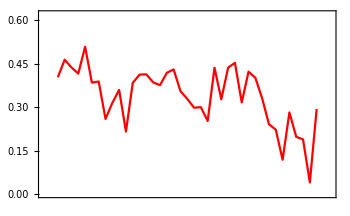
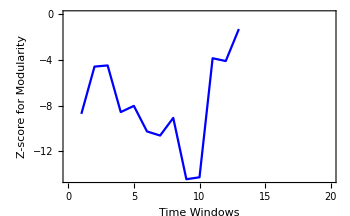
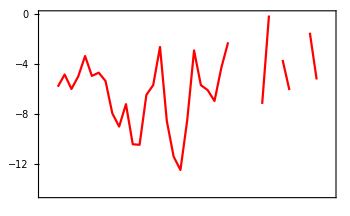

```mathematica
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{0,0.62}}],ListLinePlot[Thread[{Range@win2,modularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{0,0.62}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,singlerandomcommmodularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{0,0.62}}],ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{0,0.62}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,Zscoresmodularity1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-score for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},MinMax[{Zscoresmodularity1/.Indeterminate->0,Zscoresmodularity2/.Indeterminate->0}]}],ListLinePlot[Thread[{Range@win2,Zscoresmodularity2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},MinMax[{Zscoresmodularity1/.Indeterminate->0,Zscoresmodularity2/.Indeterminate->0}]}]}]}
```

Fixed Bucket Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket1=snetworkdatafxdbucketintimewindows[data1,9,90,win1];]
```

{6.94699,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedbucket1[[1]][[i]],widthdataintimewindowsFixedbucket1[[2]][[i]],1.5,7,400,Green],{i,Range@win1}];
modularityvalues1=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity1=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{425.098,Null}

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket2=snetworkdatafxdbucketintimewindows[data2,9,90,win2];]
```

{6.95944,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedbucket2[[1]][[i]],widthdataintimewindowsFixedbucket2[[2]][[i]],1.5,7,400,Green],{i,Range@win2}];
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity2=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{897.854,Null}

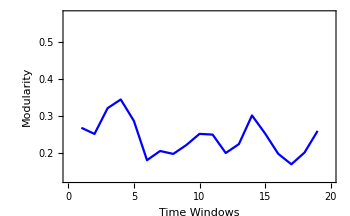
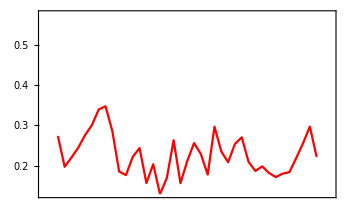
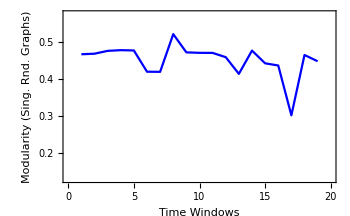
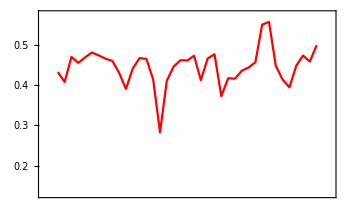
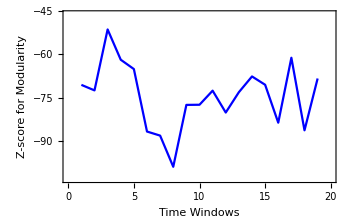
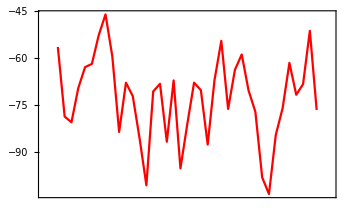

```mathematica
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{0.13,0.575}}],ListLinePlot[Thread[{Range@win2,modularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{0.13,0.575}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,singlerandomcommmodularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{0.13,0.575}}],ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{0.13,0.575}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,Zscoresmodularity1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-score for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},MinMax[{Zscoresmodularity1,Zscoresmodularity2}]}],ListLinePlot[Thread[{Range@win2,Zscoresmodularity2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},MinMax[{Zscoresmodularity1,Zscoresmodularity2}]}]}]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket1=snetworkdatafxdbucketintimewindows[data1,10,22,win1];]
```

{6.18221,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket1[[1]][[i]],thicknessdataintimewindowsFixedbucket1[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win1}];
modularityvalues1=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity1=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{154.515,Null}

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket2=snetworkdatafxdbucketintimewindows[data2,10,18,win2];]
```

{4.2987,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket2[[1]][[i]],thicknessdataintimewindowsFixedbucket2[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win2}];
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity2=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{395.841,Null}

```mathematica
Zscoresmodularity1=ReplacePart[Zscoresmodularity1,Position[Table[Head@i,{i,Zscoresmodularity1}],Times]->""]
Zscoresmodularity2=ReplacePart[Zscoresmodularity2,Position[Table[Head@i,{i,Zscoresmodularity2}],Times]->""]
```

{-4.52996,-4.72063,-2.64333,-2.69464,,-8.03465,-8.84539,-6.53786,-0.680447,-5.30417,-4.83547,-4.92529,-5.36978,-4.67555,-1.57759,-4.82477,-3.05086,-0.147881,-3.83966}

{-1.62261,-3.14707,-1.57988,-4.50942,-3.81348,0.699989,1.06675,,0.525761,-0.471981,-5.11838,-6.88725,-7.26708,0.893603,-5.89705,-5.32446,,-4.42071,-6.90075,-4.76161,-2.54575,,-0.689325,,-3.96284,-4.82491,-4.05111,-4.39764,,-3.42433,-3.02808,2.40575,0.663786,2.62412,1.59801,,-4.04504,-3.47688,-4.73253}

```mathematica
singlerandomcommmodularityvalues1=ReplacePart[singlerandomcommmodularityvalues1,Position[singlerandomcommmodularityvalues1,0]->""]
singlerandomcommmodularityvalues2=ReplacePart[singlerandomcommmodularityvalues2,Position[singlerandomcommmodularityvalues2,0]->""]
```

{0.446563,0.512731,0.423042,0.4526,,0.414028,0.418271,0.421514,0.565,0.439835,0.393996,0.384497,0.421658,0.381322,0.48615,0.41238,0.450327,0.572778,0.325713}

{0.459961,0.466942,0.413495,0.416437,0.391527,0.587674,0.540428,,0.437557,0.514403,0.408571,0.307164,0.33672,0.402188,0.377968,0.328015,,0.422661,0.472882,0.320733,0.339381,,0.435059,,0.408854,0.472973,0.355443,0.391563,,0.402778,0.371537,0.576,0.5224,0.461451,0.495868,,0.398926,0.378744,0.406142}

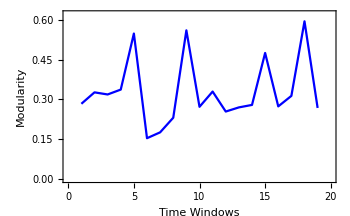
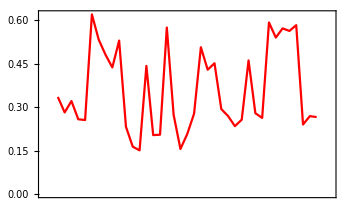
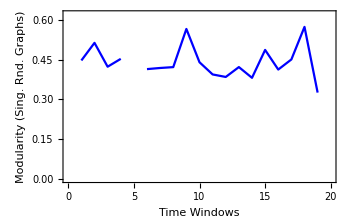
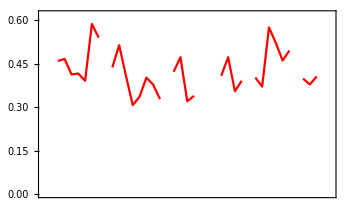
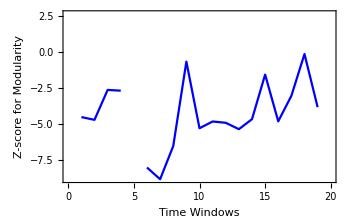
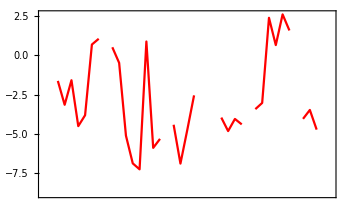

```mathematica
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},MinMax[{modularityvalues1,singlerandomcommmodularityvalues1/.""->0,modularityvalues2,singlerandomcommmodularityvalues2/.""->0}]}],ListLinePlot[Thread[{Range@win2,modularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},MinMax[{modularityvalues1,singlerandomcommmodularityvalues1/.""->0,modularityvalues2,singlerandomcommmodularityvalues2/.""->0}]}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,singlerandomcommmodularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},MinMax[{modularityvalues1,singlerandomcommmodularityvalues1/.""->0,modularityvalues2,singlerandomcommmodularityvalues2/.""->0}]}],ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},MinMax[{modularityvalues1,singlerandomcommmodularityvalues1/.""->0,modularityvalues2,singlerandomcommmodularityvalues2/.""->0}]}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,Zscoresmodularity1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-score for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},MinMax[{Zscoresmodularity1/.""->0,Zscoresmodularity2/.""->0}]}],ListLinePlot[Thread[{Range@win2,Zscoresmodularity2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},MinMax[{Zscoresmodularity1/.""->0,Zscoresmodularity2/.""->0}]}]}]}
```